# Report Project 1

Course code: IX1500
Date: 2022-09-16

Muttakin Karim, muttakin@kth.se
Samir Alami, samirala@kth.se

Task 1: Texas Hold’em

## Summary

### Task

In the Texas hold ‘em poker game every player gets just two cards (hole cards), while the best hand is determined by the combination of any five cards chosen from your two face down “hole” cards and the five face up “community” cards (shared by all players). 
The problem consist of determining the exact probability of the hands below (best hand possible), using the census method (2.4 above), when a player has two specific “hole” cards and the community cards are unknown. This is the situation in the first pre-flop (before dealing the community cards) betting round in Texas hold ‘em. Chose the specific “hole” cards at random.

After this choose three of the five “community cards” at random and redo the calculation of the probabilities. Keep the specific “hole cards” you had. This is the situation of the second betting round. Compare the pre-flop probabilities with the situation where three of the “community cards” are known and discuss the results.

The deck is a normal 52 card deck without any jokers.

one pair

two pairs

three of a kind

straight

flush

full house

four of a kind

straight flush

royal straight flush

### Results

#### Pre-flop

One pair		47.85%

Two pairs		22.99%

Three of a kind		4.589%

Straight		2.980%

Flush			1.972%

Full house		0.478%

Four of a kind		0.463%

Straight flush		0.1038%

Royal straight flush	0.003681%

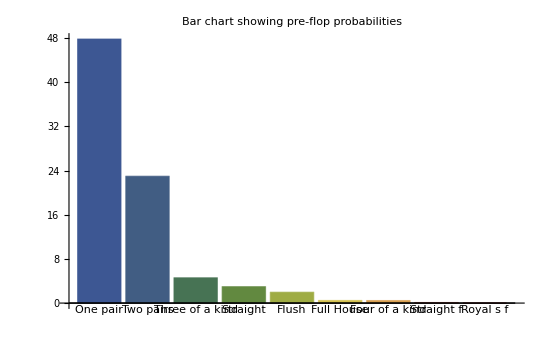

```mathematica
Diagram
```

#### Flop

One pair		48.84%

Two pairs		8.326%

Three of a kind		1.388%

Straight		0%

Flush			0%

Full house		0%

Four of a kind		0%

Straight flush		0%

Royal straight flush	0%

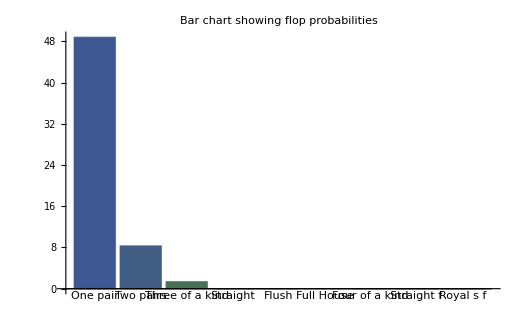

```mathematica
Diagram
```

## Code for pre-flop

### Initialization

First the deck was created where each card was given its suit and value. The once and the tenth digit describes its value and the hundredth digit its suit. Therefore modolus 100 and division 100 was used to get the respective type.

```mathematica
ClearAll["'*"]
```

```mathematica
♣=Range[101,113];
```

```mathematica
♢=Range[201,213];
```

```mathematica
♡=Range[301,313];
```

```mathematica
♠=Range[401,413];
```

```mathematica
deck=Join[♣,♢,♡,♠];
```

```mathematica
hand=RandomChoice[deck,2]
```

{101,212}

```mathematica
deckWithoutChosenHand=Cases[deck,Except[Alternatives@@hand]];
```

```mathematica
subsetsOf50Cards=Sort[Subsets[deckWithoutChosenHand,{5}]];
```

```mathematica
combination=Sort[Flatten[Append[#,hand]]]&/@subsetsOf50Cards;
```

### One pair

To get a specific pair first we defined a pattern which included the specfic pair and excluded all other all other possibilities. The same method has been used in all other calculations.

```mathematica
onePairQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
onePairQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
onePairQ[{___, x_, x_, x_, ___}] := False;
onePairQ[{___, x_, ___,x_,___}] := True;
onePairQ[{___}] := False;
```

```mathematica
onePair[hole_]:=onePairQ[Sort[Mod[hole,100]]]
```

```mathematica
onePairProbability=Count[combination, _?(onePair)]/Length[combination]
```

25344/52969

```mathematica
PercentForm[N[onePairProbability]]
```

47.85%

### Two pairs

```mathematica
twoPairQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
twoPairQ[{___, x_, x_, x_, ___}] := False;
twoPairQ[{___ ,x_, x_,___}] := False;
twoPairQ[{___}] := False;
twoPairQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := True;
```

```mathematica
twoPair[hole_]:=twoPairQ[Sort[Mod[hole,100]]]
```

```mathematica
twoPairProbability=Count[combination, _?(twoPair)]/Length[combination]
```

12177/52969

```mathematica
PercentForm[N[twoPairProbability]]
```

22.99%

### Three of a kind

```mathematica
threeQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
threeQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
threeQ[{___, x_, x_, x_, ___}] := True;
threeQ[{___, x_,___, x_, x_,  ___}] := False;
threeQ[{___}] := False;
```

```mathematica
three[hole_]:=threeQ[Sort[Mod[hole,100]]]
```

```mathematica
threeProbability=Count[combination, _?(three)]/Length[combination]
```

2431/52969

```mathematica
PercentForm[N[threeProbability]]
```

4.589%

### Straight

```mathematica
straight [hole_]:=MatchQ[hole-hole⟦1⟧,{0,1,2,3,4,___}]||MatchQ[hole-hole⟦2⟧,{_,0,1,2,3,4,_}]||MatchQ[hole-hole⟦3⟧,{___,0,1,2,3,4}]||MatchQ[hole,{1,___,10,11,12,13}]
```

```mathematica
combinationValue=Sort[Mod[combination,100]];
```

```mathematica
combinationValueSorted=Map[Sort,combinationValue];
```

```mathematica
straightProbability=Count[combinationValueSorted,_?(straight)]/Length[combinationValue]
```

7892/264845

```mathematica
PercentForm[N[straightProbability]]
```

2.98%

### Flush

```mathematica
flushQ[{___}] := False;
flushQ[{___, x_, x_, x_, x_, x_, ___}] := True;
flush[h_]:=flushQ[Sort[Mod[h,100]]]
```

```mathematica
combinationColor=Sort[Quotient[combination,100]];
```

```mathematica
flushProbability=Count[combinationColor,_?(flush)]/Length[combinationColor]
```

20889/1059380

```mathematica
PercentForm[N[flushProbability]]
```

1.972%

### Full house

```mathematica
fullHouseQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := True;
fullHouseQ[{___, x_, x_, x_, y_, y_, ___}/;x≠y] := True;
fullHouseQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
fullHouseQ[{___, x_, x_, x_, x_, ___, ___}] := False;
fullHouseQ[{___, x_, x_, x_, ___, ___, ___}] := False;
fullHouseQ[{___, x_, x_, ___}] := False;
fullHouseQ[{___}] := False;
fullHouse[h_]:=fullHouseQ[Sort[Mod[h,100]]]
```

```mathematica
fullHouseProbability=Count[combinationValue,_?(fullHouse)]/Length[combinationValue]
```

981/211876

```mathematica
PercentForm[N[fullHouseProbability]]
```

0.463%

### Four of a kind

```mathematica
fourQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
fourQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
fourQ[{___, x_, x_, x_, x_, ___, ___}] := True;
fourQ[{___, x_, x_, x_, ___}] := False;
fourQ[{___, ___, ___, x_, x_, ___, ___}] := False;
fourQ[{___}] := False;
four[h_]:=fourQ[Sort[Mod[h,100]]]
```

```mathematica
fourProbability=Count[combination,_?(four)]/Length[combination]
```

55/52969

```mathematica
PercentForm[N[fourProbability]]
```

0.1038%

### Straight flush

```mathematica
straightFlushQ [hole_]:=MatchQ[hole-hole⟦1⟧,{0,1,2,3,4,_,_}]||MatchQ[hole-hole⟦2⟧,{_,0,1,2,3,4,_}]||MatchQ[hole-hole⟦3⟧,{_,_,0,1,2,3,4}]||MatchQ[hole,{1,_,_,10,11,12,13}]
```

```mathematica
straightFlushProbability=Count[combination,_?(straightFlushQ)]/Length[combination]
```

3/37835

```mathematica
PercentForm[N[straightFlushProbability]]
```

0.007929%

### Royal straight flush

```mathematica
royalStraightFlushQ [hole_]:=MatchQ[hole-hole⟦1⟧,{0,9,10,11,12,___}]||MatchQ[hole-hole⟦2⟧,{_,0,9,10,11,12,_}]||MatchQ[hole-hole⟦3⟧,{___,0,9,10,11,12}]||MatchQ[hole,{1,___,10,11,12,13}]
```

```mathematica
royalStraightFlushProbability=Count[combination,_?(royalStraightFlushQ)]/Length[combination]
```

39/1059380

```mathematica
PercentForm[N[royalStraightFlushProbability]]
```

0.003681%

Code for diagram

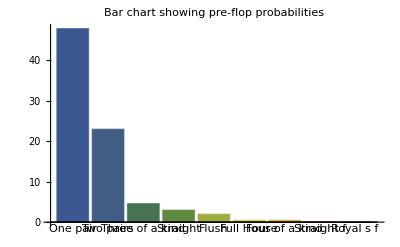

```mathematica
BarChart[{47.85,22.99,4.589,2.980,1.972,0.478,0.463,0.1038,0.003681},ChartLabels->{"One pair","Two pairs","Three of a kind","Straight","Flush","Full House","Four of a kind","Straight f","Royal s f"},ChartStyle->"DarkRainbow",PlotLabel->Style["Bar chart showing pre-flop probabilities",FontSize->18]]
```

## Code for flop

### Initialization

```mathematica
deckWithoutChosenHand=Cases[deck,Except[Alternatives@@hand]];
```

```mathematica
community=RandomChoice[deckWithoutChosenHand,3]
```

{407,409,204}

```mathematica
flopHand=Join[hand,community]
```

{101,212,407,409,204}

```mathematica
deckWithoutFlopHand=Cases[deck,Except[Alternatives@@flopHand]];
```

```mathematica
subsetsOf47Cards=Sort[Subsets[deckWithoutFlopHand,{2}]];
```

```mathematica
combinationFlop=Sort[Flatten[Append[#,flopHand]]]&/@subsetsOf47Cards;
```

### One pair

```mathematica
onePairFlopQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
onePairFlopQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
onePairFlopQ[{___, x_, x_, x_, ___}] := False;
onePairFlopQ[{___, x_, ___,x_,___}] := True;
onePairFlopQ[{___}] := False;
```

```mathematica
onePairFlop[hole_]:=onePairFlopQ[Sort[Mod[hole,100]]]
```

```mathematica
onePairProbabilityFlop=Count[combinationFlop, _?(onePairFlop)]/Length[combinationFlop]
```

528/1081

```mathematica
PercentForm[N[onePairProbabilityFlop]]
```

48.84%

### Two pairs

```mathematica
twoPairFlopQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
twoPairFlopQ[{___, x_, x_, x_, ___}] := False;
twoPairFlopQ[{___ ,x_, x_,___}] := False;
twoPairFlopQ[{___}] := False;
twoPairFlopQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := True;
```

```mathematica
twoPairFlop[hole_]:=twoPairFlopQ[Sort[Mod[hole,100]]]
```

```mathematica
twoPairFlopProbability=Count[combinationFlop, _?(twoPairFlop)]/Length[combinationFlop]
```

90/1081

```mathematica
PercentForm[N[twoPairFlopProbability]]
```

8.326%

### Three of a kind

```mathematica
threeFlopQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
threeFlopQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
threeFlopQ[{___, x_, x_, x_, ___}] := True;
threeFlopQ[{___, x_,___, x_, x_,  ___}] := False;
threeFlopQ[{___}] := False;
```

```mathematica
threeFlop[hole_]:=threeFlopQ[Sort[Mod[hole,100]]]
```

```mathematica
threeFlopProbability=Count[combinationFlop, _?(threeFlop)]/Length[combinationFlop]
```

15/1081

```mathematica
PercentForm[N[threeFlopProbability]]
```

1.388%

### Straight

```mathematica
straightFlop [hole_]:=MatchQ[hole-hole⟦1⟧,{0,1,2,3,4,___}]||MatchQ[hole-hole⟦2⟧,{_,0,1,2,3,4,_}]||MatchQ[hole-hole⟦3⟧,{___,0,1,2,3,4}]||MatchQ[hole,{1,___,10,11,12,13}]
```

```mathematica
combinationFlopValue=Sort[Mod[combinationFlop,100]];
```

```mathematica
combinationFlopValueSorted=Map[Sort,combinationFlopValue];
```

```mathematica
straightFlopProbability=Count[combinationFlopValueSorted,_?(straightFlop)]/Length[combinationFlopValue]
```

0

```mathematica
PercentForm[N[straightFlopProbability]]
```

0%

### Flush

```mathematica
flushFlopQ[{___}] := False;
flushFlopQ[{___, x_, x_, x_, x_, x_, ___}] := True;
flushFlop[h_]:=flushFlopQ[Sort[Mod[h,100]]]
```

```mathematica
combinationFlopColor=Sort[Quotient[combinationFlop,100]];
```

```mathematica
flushFlopProbability=Count[combinationFlopColor,_?(flushFlop)]/Length[combinationFlopColor]
```

0

```mathematica
PercentForm[N[flushFlopProbability]]
```

0%

### Full house

```mathematica
fullHouseFlopQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := True;
fullHouseFlopQ[{___, x_, x_, x_, y_, y_, ___}/;x≠y] := True;
fullHouseFlopQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
fullHouseFlopQ[{___, x_, x_, x_, x_, ___, ___}] := False;
fullHouseFlopQ[{___, x_, x_, x_, ___, ___, ___}] := False;
fullHouseFlopQ[{___, x_, x_, ___}] := False;
fullHouseFlopQ[{___}] := False;
fullHouseFlop[h_]:=fullHouseFlopQ[Sort[Mod[h,100]]]
```

```mathematica
fullHouseFlopProbability=Count[combinationFlopValue,_?(fullHouseFlop)]/Length[combinationFlopValue]
```

0

```mathematica
PercentForm[N[fullHouseFlopProbability]]
```

0%

### Four of a kind

```mathematica
fourFlopQ[{x_,x_, x_, y_, y_, y_, ___}/;x≠y] := False;
fourFlopQ[{___, x_,x_, ___, y_, y_, ___}/;x≠y] := False;
fourFlopQ[{___, x_, x_, x_, x_, ___, ___}] := True;
fourFlopQ[{___, x_, x_, x_, ___}] := False;
fourFlopQ[{___, ___, ___, x_, x_, ___, ___}] := False;
fourFlopQ[{___}] := False;
fourFlop[h_]:=fourFlopQ[Sort[Mod[h,100]]]
```

```mathematica
fourFlopProbability=Count[combinationFlop,_?(fourFlop)]/Length[combinationFlop]
```

0

```mathematica
PercentForm[N[fourFlopProbability]]
```

0%

### Straight flush

```mathematica
straightFlushFlopQ[hole_]:=MatchQ[hole-hole⟦1⟧,{0,1,2,3,4,_,_}]||MatchQ[hole-hole⟦2⟧,{_,0,1,2,3,4,_}]||MatchQ[hole-hole⟦3⟧,{_,_,0,1,2,3,4}]||MatchQ[hole,{1,_,_,10,11,12,13}]
```

```mathematica
straightFlushFlopProbability=Count[combinationFlop,_?(straightFlushFlopQ)]/Length[combinationFlop]
```

0

```mathematica
PercentForm[N[straightFlushFlopProbability]]
```

0%

### Royal straight flush

```mathematica
royalStraightFlushFlopQ[hole_]:=MatchQ[hole-hole⟦1⟧,{0,9,10,11,12,___}]||MatchQ[hole-hole⟦2⟧,{_,0,9,10,11,12,_}]||MatchQ[hole-hole⟦3⟧,{___,0,9,10,11,12}]||MatchQ[hole,{1,___,10,11,12,13}]
```

```mathematica
royalStraightFlushFlopProbability=Count[combinationFlop,_?(royalStraightFlushFlopQ)]/Length[combinationFlop]
```

0

```mathematica
PercentForm[N[royalStraightFlushFlopProbability]]
```

0%

```mathematica
Code for diagram
```

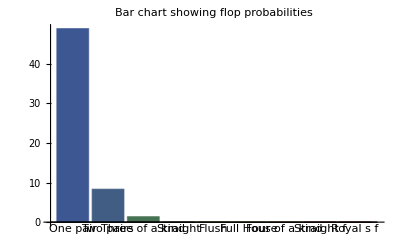

```mathematica
BarChart[{48.84,8.326,1.388,0,0,0,0,0,0},ChartLabels->{"One pair","Two pairs","Three of a kind","Straight","Flush","Full House","Four of a kind", "Straight f", "Royal s f"},ChartStyle->"DarkRainbow",PlotLabel->Style["Bar chart showing flop probabilities", FontSize->18]]
```

## Discussion

The pre-flop was calculated with 2 hole cards with 5 of the community cards unknown. The best hand was calculated using the census method which was described in detailed instructions in the question. The combination was done with the 50 cards which were unknown to the players. The hole cards were chosen randomly with RandomChoice[] function. Then the subset of the 50 cards were combined with the hole cards, this combination was used to calculate the probabilites of the different hands. 
The flop was calculated with the same 2 hole cards and 3 community cards visible to the player. This ment that now the best hand will have to calculated with a total of 5 out of the 7 cards. In this case the number of cards left in the deck was 47. So the combination of 47 cards with the hole and the community cards gave the probabilites of the flop. The probablities varied depending on which hole cards and the community cards the player has received. The hole cards during this simulation were ace of clubs and queen of diamonds, the community cards were seven, nine of spades and 4 of diamonds. In this case, it can instantly be seen that the chances of getting a flush, straight flush,  four of a kind, straight flush and royal straight fulsh is zero. This was confirmed by the calculated probability. But during the pre-flop stage the probability was higher as less cards were visible. Therefore, the probability in this game depends on the hole cards and the community cards.

A drawback of  this whole simulation is that Texas hold’em is played with at least two players. This means that during an actual game the overall probabilities of getting a hand at any stage of the game is going to less than the ones that are calculated. Additionally, en exemption has been made while simulating the flush hand. It was assumed that the pairs of ones and twos would not interfere while calculating the final probabiltiy, but in reality this is not the case. 

In conclusion, this model helped to understand how a game of cards can be simulated using combinatorics and set theory. The concept of  managing probabilty was also explored in this simulation. This helped to deepen the understanding of various outcomes of different types of experiments.